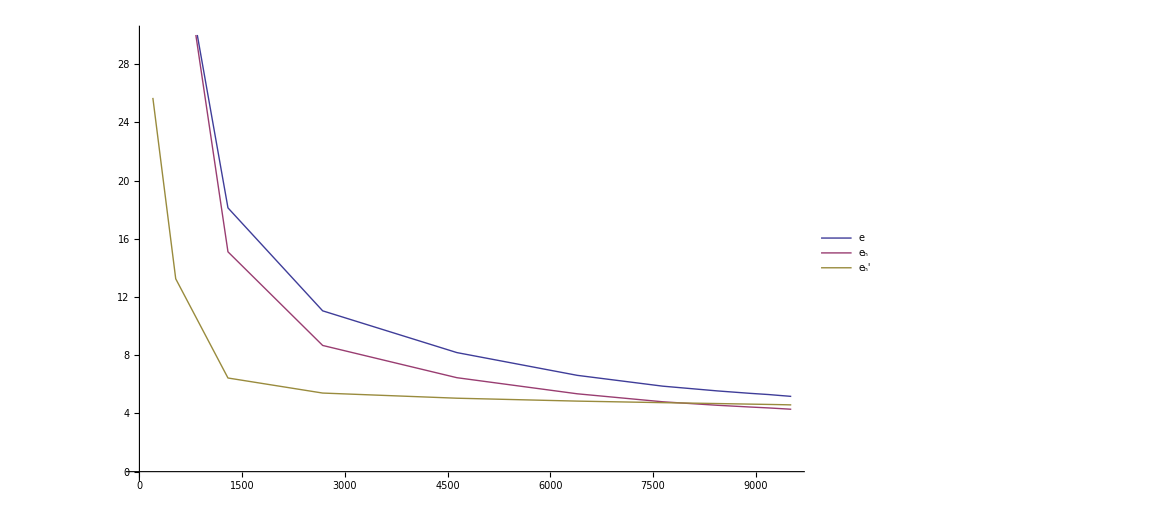

```mathematica
SetDirectory["d:\\Learn\\Diploma\\DiplomaText\\include\\8NumResults\\problem2\\my\\errors\\"];
triangles = Import["triangles.txt","List"];
realErr = Import["realError.txt","List"];
myErr = Import["myError.txt","List"];
ostErr = Import["ostError.txt","List"];

t[x_,y_] = x^14 y  (1-x ) (1-y);
u[x_,y_ ]=t[x,y]+t[y,x];
q[x_,y_] = u[x,y]^2+D[u[x,y],x]^2+D[u[x,y],y]^2;
norm = Sqrt[Integrate[q[x,y],{x,0,1},{y,0,1}]]/100;


ListLinePlot[{
	Transpose[{triangles, realErr/norm}],
	Transpose[{triangles, myErr/norm}],
	Transpose[{triangles, ostErr/norm}]
},
PlotLegends->Placed[{
ToExpression["e",TeXForm,HoldForm],
ToExpression["e_h",TeXForm,HoldForm],
ToExpression["e_h^\prime",TeXForm,HoldForm]
},{0.8,.5}],
BaseStyle->{FontWeight->"Bold",FontSize->20},
PlotRange -> {0,30}
]
```

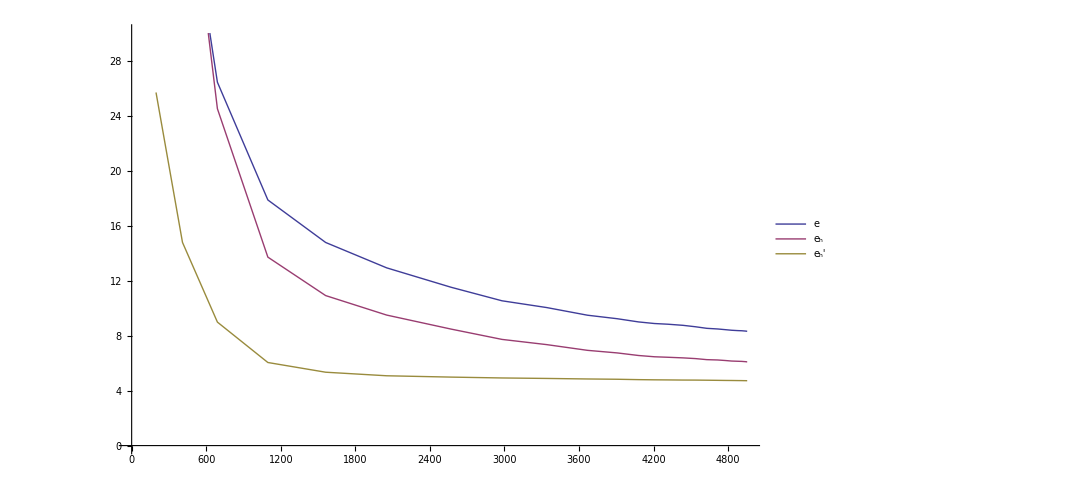

```mathematica
SetDirectory["d:\\Learn\\Diploma\\DiplomaText\\include\\8NumResults\\problem2\\ost\\errors\\"];
triangles = Import["triangles.txt","List"];
realErr = Import["realError.txt","List"];
myErr = Import["myError.txt","List"];
ostErr = Import["ostError.txt","List"];

ListLinePlot[{
	Transpose[{triangles, realErr/norm}],
	Transpose[{triangles, myErr/norm}],
	Transpose[{triangles, ostErr/norm}]
},

PlotLegends->Placed[{
ToExpression["e",TeXForm,HoldForm],
ToExpression["e_h",TeXForm,HoldForm],
ToExpression["e_h^\prime",TeXForm,HoldForm]
},{0.8,.5}],
BaseStyle->{FontWeight->"Bold",FontSize->20},
PlotRange -> {0,30},
PlotStyle->{Thickness->0.004,Thickness->0.004,Thickness->0.004},
AxesLabel->{"","%"}
]
```